```mathematica
(*n阶Haar小波在x处的函数值*)
hmx[n_,x_]:=Module[{j,k},
If[n==0,If[0≤x≤1,Return[1],Return[0]],
j=0;
While[True,If[n≥2^j,j++,Break[]]];
j=j-1;
k=n-2^j;
If[0≤2^j x-k<1/2,Return[1],
If[1/2≤2^j x-k<1,Return[-1],Return[0]]
]
]
]
```

```mathematica
(*生成m阶积分算子,m=2^j*) 
integrate[m_]:=Module[{pm,hm2,hm2inverse,temp,i,j},
If[m==1,pm={1/2};Return[pm],
If[m==2,pm={{1/2,-1/4},{1/4,0}};Return[pm],
pm=Table[m,{i,1,m},{j,1,m}];
temp=integrate[m/2];
hm2=Table[hmx[Mod[i-1,m/2],(2 j-1)/m],{i,1,m/2},{j,1,m/2}];
hm2inverse=Inverse[hm2];
For[i=1,i≤m/2,i++,
For[j=1,j≤m/2,j++,
pm[[i,j]]=temp[[i,j]];
pm[[i,j+m/2]]=-hm2[[i,j]]/(2 m);
pm[[i+m/2,j+m/2]]=0;
pm[[i+m/2,j]]=hm2inverse[[i,j]]/(2 m);
]];
Return[pm]
]
]
]
```

```mathematica
(*t=0时，u关于x的两阶导*)
u2dx[x_]:=-4 Pi^2 Sin[2 Pi x];
(*生成x点处m阶小波函数向量*)
hmxcolumn[m_,x_]:=Module[{temp,i},
temp=Table[hmx[i,x],{i,0,m-1}];
temp];
```

```mathematica
(*对时间t的离散*)
deltat=N[1/10000];
(*逼近的阶数*)
j=5;
m=2^j;
(*计算积分算子矩阵*)
pm=integrate[m];
xl=Table[i/(m),{i,1,32}];
(*求解小波系数所需要的矩阵*)
coeffmatrix=Table[deltat*hmxcolumn[m,xl[[i]]]-4*Pi^2*pm.pm.(hmxcolumn[m,xl[[i]]]-xl[[i]]*hmxcolumn[m,1]),{i,1,m}];
(*初始边界条件向量*)
u2dx0=N[-u2dx[xl]];
(*求解小波系数*)
cmts=Inverse[coeffmatrix].u2dx0;
(*u''(xl,t_{s+1})的值，用于下一次迭代求解*)
u2dxxlts1=Table[deltat*cmts.hmxcolumn[m,xl[[i]]],{i,1,m}]+u2dx0;
(*t=ts时该时间层 数值解*)
uxlts1=Table[deltat*pm.pm.(hmxcolumn[m,xl[[i]]]-xl[[i]]*hmxcolumn[m,1]),{i,1,m}].cmts+u[xl,0];
```

```mathematica
(*精确解*)
u[x_,t_]:=E^(-t)*Sin[2 Pi x];
correctuxlts1=N[u[xl,0]];
```

```mathematica
(*计算误差*)
list=Table[{xl[[i]],correctuxlts1[[i]],uxlts1[[i]],Abs[correctuxlts1[[i]]-uxlts1[[i]]]},{i,1,m,2}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
1/32 | 0.19509 | 0.195071 | 0.000019507
3/32 | 0.55557 | 0.555515 | 0.0000555512
5/32 | 0.83147 | 0.831386 | 0.0000831382
7/32 | 0.980785 | 0.980687 | 0.000098068
9/32 | 0.980785 | 0.980687 | 0.0000980677
11/32 | 0.83147 | 0.831386 | 0.0000831371
13/32 | 0.55557 | 0.555515 | 0.0000555491
15/32 | 0.19509 | 0.195071 | 0.0000195036
17/32 | -0.19509 | -0.195071 | 0.0000195124
19/32 | -0.55557 | -0.555515 | 0.0000555594
21/32 | -0.83147 | -0.831386 | 0.0000831506
23/32 | -0.980785 | -0.980687 | 0.0000980867
25/32 | -0.980785 | -0.980687 | 0.0000980959
27/32 | -0.83147 | -0.831386 | 0.0000831795
29/32 | -0.55557 | -0.555515 | 0.0000556131
31/32 | -0.19509 | -0.195071 | 0.0000195998

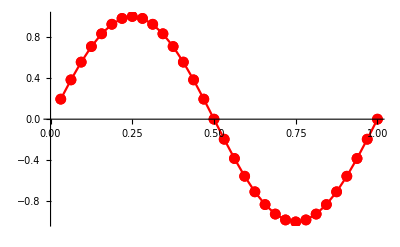

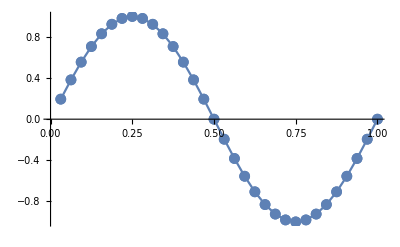

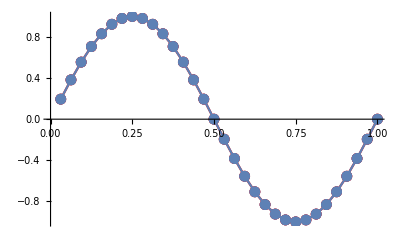

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xl[[i]],uxlts1[[i]]},{i,1,m}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xl[[i]],correctuxlts1[[i]]},{i,1,m}],Mesh->Full]
(*对比图*)
Show[img1,img2]
```

```mathematica
(*对时间t的离散*)
deltat=N[1/10000];
(*逼近的阶数*)
j=6;
m=2^j;
(*计算积分算子矩阵*)
pm=integrate[m];
xl=N[Table[i/(m),{i,1,m}]];
(*求解小波系数所需要的矩阵*)
coeffmatrix=Table[deltat*hmxcolumn[m,xl[[i]]]-4*Pi^2*pm.pm.(hmxcolumn[m,xl[[i]]]-xl[[i]]*hmxcolumn[m,1]),{i,1,m}];
(*初始边界条件向量*)
u2dx0=N[-u2dx[xl]];
(*求解小波系数*)
cmts=Inverse[coeffmatrix].u2dx0;
(*u''(xl,t_{s+1})的值，用于下一次迭代求解*)
u2dxxlts1=Table[deltat*cmts.hmxcolumn[m,xl[[i]]],{i,1,m}]+u2dx0;
(*t=ts时该时间层 数值解*)
uxlts1=Table[deltat*pm.pm.(hmxcolumn[m,xl[[i]]]-xl[[i]]*hmxcolumn[m,1]),{i,1,m}].cmts+u[xl,0];
(*精确解*)
correctuxlts1=N[u[xl,0]];
```

```mathematica
(*计算误差*)
list=Table[{xl[[i]],correctuxlts1[[i]],uxlts1[[i]],Abs[correctuxlts1[[i]]-uxlts1[[i]]]},{i,1,m,2}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
0.015625 | 0.0980171 | 0.0980073 | 9.80073×10^-6
0.046875 | 0.290285 | 0.290256 | 0.0000290256
0.078125 | 0.471397 | 0.47135 | 0.000047135
0.109375 | 0.634393 | 0.63433 | 0.000063433
0.140625 | 0.77301 | 0.772933 | 0.0000772933
0.171875 | 0.881921 | 0.881833 | 0.0000881833
0.203125 | 0.95694 | 0.956845 | 0.0000956844
0.234375 | 0.995185 | 0.995085 | 0.0000995085
0.265625 | 0.995185 | 0.995085 | 0.0000995085
0.296875 | 0.95694 | 0.956845 | 0.0000956844
0.328125 | 0.881921 | 0.881833 | 0.0000881833
0.359375 | 0.77301 | 0.772933 | 0.0000772933
0.390625 | 0.634393 | 0.63433 | 0.000063433
0.421875 | 0.471397 | 0.47135 | 0.000047135
0.453125 | 0.290285 | 0.290256 | 0.0000290256
0.484375 | 0.0980171 | 0.0980073 | 9.80073×10^-6
0.515625 | -0.0980171 | -0.0980073 | 9.80073×10^-6
0.546875 | -0.290285 | -0.290256 | 0.0000290256
0.578125 | -0.471397 | -0.47135 | 0.000047135
0.609375 | -0.634393 | -0.63433 | 0.000063433
0.640625 | -0.77301 | -0.772933 | 0.0000772933
0.671875 | -0.881921 | -0.881833 | 0.0000881833
0.703125 | -0.95694 | -0.956845 | 0.0000956845
0.734375 | -0.995185 | -0.995085 | 0.0000995087
0.765625 | -0.995185 | -0.995085 | 0.000099509
0.796875 | -0.95694 | -0.956845 | 0.0000956856
0.828125 | -0.881921 | -0.881833 | 0.000088186
0.859375 | -0.77301 | -0.772933 | 0.0000772995
0.890625 | -0.634393 | -0.63433 | 0.0000634472
0.921875 | -0.471397 | -0.47135 | 0.0000471674
0.953125 | -0.290285 | -0.290256 | 0.0000290997
0.984375 | -0.0980171 | -0.0980072 | 9.97011×10^-6

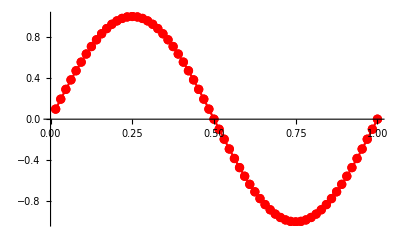

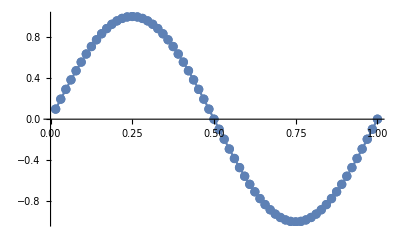

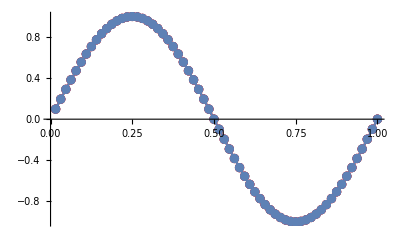

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xl[[i]],uxlts1[[i]]},{i,1,m}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xl[[i]],correctuxlts1[[i]]},{i,1,m}],Mesh->Full]
(*对比图*)
Show[img1,img2]
```

```mathematica
(*对时间t的离散*)
deltat=N[1/1000];
(*逼近的阶数*)
j=4;
m=2^j;
(*计算积分算子矩阵*)
pm=integrate[m];
(*离散点，为求解系数构造足够的方程*)
xl=N[Table[i/(m),{i,1,m}]];
(*求解小波系数所需要的矩阵*)
coeffmatrix=Table[-deltat^2/2*hmxcolumn[m,xl[[i]]]+pm.pm.hmxcolumn[m,xl[[i]]],{i,1,m}];
(*初始边界条件向量*)
u2dx0=xl*Pi^3*Cos[Pi*deltat]-Pi^2*Sin[Pi*xl];
(*求解小波系数*)
cmts=Inverse[coeffmatrix].u2dx0;
(*(*u''(xl,t_{s+1})的值，用于下一次迭代求解*)
u2dxxlts1=Table[deltat*cmts.hmxcolumn[m,xl[[i]]],{i,1,m}]+u2dx0;*)
(*t=ts时该时间层 数值解*)
uxlts1=Table[deltat^2/2*pm.pm.hmxcolumn[m,xl[[i]]],{i,1,m}].cmts+xl*(Pi*Cos[Pi deltat]-Pi)+Sin[Pi xl];
(*精确解*)
correctuxlts1=N[Cos[Pi*deltat]*Sin[Pi*xl]];
```

```mathematica
(*计算误差*)
list=Table[{xl[[i]],correctuxlts1[[i]],uxlts1[[i]],Abs[correctuxlts1[[i]]-uxlts1[[i]]]},{i,1,m,2}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
0.0625 | 0.195089 | 0.195089 | 3.72873×10^-7
0.1875 | 0.555567 | 0.555566 | 1.12168×10^-6
0.3125 | 0.831466 | 0.831464 | 1.87968×10^-6
0.4375 | 0.98078 | 0.980778 | 2.65311×10^-6
0.5625 | 0.98078 | 0.980777 | 3.44829×10^-6
0.6875 | 0.831466 | 0.831461 | 4.27175×10^-6
0.8125 | 0.555567 | 0.555562 | 5.13024×10^-6
0.9375 | 0.195089 | 0.195083 | 6.03081×10^-6

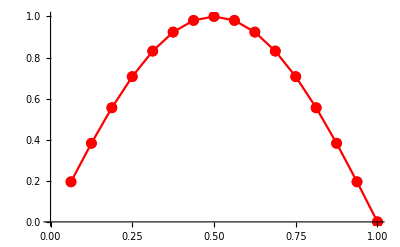

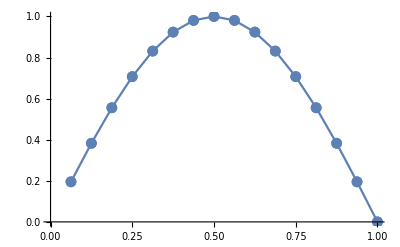

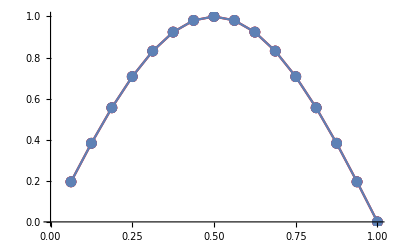

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xl[[i]],uxlts1[[i]]},{i,1,m}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xl[[i]],correctuxlts1[[i]]},{i,1,m}],Mesh->Full]
(*对比图*)
Show[img1,img2]
```

```mathematica
(*对时间t的离散*)
deltat=N[1/1000];
(*逼近的阶数*)
j=5;
m=2^j;
(*计算积分算子矩阵*)
pm=integrate[m];
(*离散点，为求解系数构造足够的方程*)
xl=N[Table[i/(m),{i,1,m}],15];
(*求解小波系数所需要的矩阵*)
coeffmatrix=Table[-deltat^2/2*hmxcolumn[m,xl[[i]]]+pm.pm.hmxcolumn[m,xl[[i]]],{i,1,m}];
(*初始边界条件向量*)
u2dx0=xl*Pi^3*Cos[Pi*deltat]-Pi^2*Sin[Pi*xl];
(*求解小波系数*)
cmts=Inverse[coeffmatrix].u2dx0;
(*(*u''(xl,t_{s+1})的值，用于下一次迭代求解*)
u2dxxlts1=Table[deltat*cmts.hmxcolumn[m,xl[[i]]],{i,1,m}]+u2dx0;*)
(*t=ts时该时间层 数值解*)
uxlts1=Table[deltat^2/2*pm.pm.hmxcolumn[m,xl[[i]]],{i,1,m}].cmts+xl*(Pi*Cos[Pi deltat]-Pi)+Sin[Pi xl];
(*精确解*)
correctuxlts1=N[Cos[Pi*deltat]*Sin[Pi*xl]];
(*计算误差*)
list=Table[{xl[[i]],correctuxlts1[[i]],uxlts1[[i]],Abs[correctuxlts1[[i]]-uxlts1[[i]]]},{i,1,m,2}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
0.03125 | 0.0980167 | 0.0980137 | 2.9304×10^-6
0.09375 | 0.290283 | 0.290274 | 8.88761×10^-6
0.15625 | 0.471394 | 0.471379 | 0.0000151372
0.21875 | 0.63439 | 0.634368 | 0.0000218849
0.28125 | 0.773007 | 0.772977 | 0.0000293527
0.34375 | 0.881917 | 0.881879 | 0.0000377863
0.40625 | 0.956936 | 0.956888 | 0.0000474631
0.46875 | 0.99518 | 0.995121 | 0.0000587016
0.53125 | 0.99518 | 0.995108 | 0.0000718715
0.59375 | 0.956936 | 0.956848 | 0.0000874061
0.65625 | 0.881917 | 0.881811 | 0.000105817
0.71875 | 0.773007 | 0.772879 | 0.000127709
0.78125 | 0.63439 | 0.634236 | 0.000153803
0.84375 | 0.471394 | 0.471209 | 0.000184958
0.90625 | 0.290283 | 0.290061 | 0.000222198
0.96875 | 0.0980167 | 0.0977499 | 0.000266749

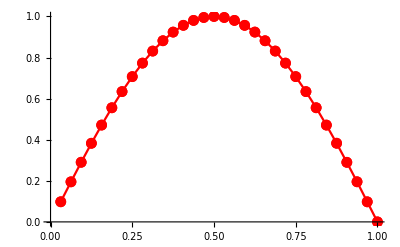

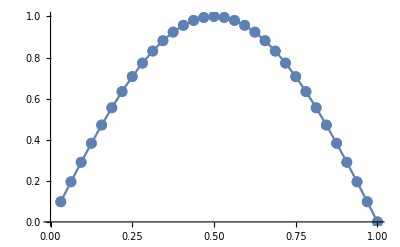

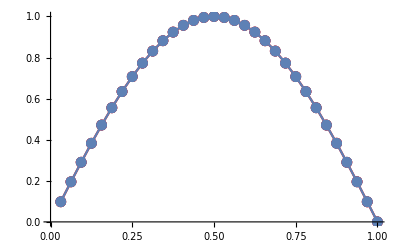

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xl[[i]],uxlts1[[i]]},{i,1,m}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xl[[i]],correctuxlts1[[i]]},{i,1,m}],Mesh->Full]
(*对比图*)
Show[img1,img2]
```

```mathematica
(*Shannon小波求解Convection-Diffusion方程*)
```

```mathematica
(*j阶Shannon小波基函数*)
w[j_,x_]:=If[x==0,0,Sin[Pi 2^j/2 x]/(Pi 2^j/2 x)];
(*一阶导*)
wdx[k_,x_]:=If[x==0,0,D[Sin[Pi 2^k/2 t]/(Pi 2^k/2 t),t]/.t->x];
(*二阶导*)
wd2x[k_,x_]:=If[x==0,0,D[Sin[Pi 2^k/2 t]/(Pi 2^k/2 t),{t,2}]/.t->x];
```

```mathematica
delta=0.0001;
epsilon=0.1;
lamuda=-0.01;
Clear[f,g0,g2];
f[x_]:=E^(-5 x) Sin[Pi x];
(*f[x_]:=E^(-(x-2)^2/8);*)
g0[t_]:=Sqrt[20/(20+t)]*E^(-(5+4t)^2/10/(t+20));
g2[t_]:=Sqrt[20/(20+t)]*E^(-2 (5+2t)^2/5/(t+20));
j=4;
xi=Table[i 2/2^j,{i,0,2^j}];
U0=f[xi];
V=Table[-epsilon wdx[j,2 (k-n)/2^j]+lamuda wd2x[j,2 (k-n)/2^j],{k,1,2^j+1},{n,1,2^j+1}];
K1=V.U0;
K2=V.(U0+K1/2);
K3=V.(U0+(Sqrt[2]-1)/2 K1+(Sqrt[2]+1)/2 K2);
K4=V.(U0-Sqrt[2]/2 K2+(2+Sqrt[2])/2 K3);
Ui1=U0+delta/6 (K1+(2-Sqrt[2]) K2+(2+Sqrt[2]) K3+K4);
```

```mathematica
(*精确解*)
Clear[u3];
u3[x_,t_]:=E^(-5 x+t (-0.01 (25-Pi^2)+0.5)) Sin[Pi x];
correctu=u3[xi,0.001];
list=Table[{N[xi[[i]]],correctu[[i]],Ui1[[i]],Abs[correctu[[i]]-Ui1[[i]]]},{i,2,2^j+1}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
0.125 | 0.204907 | 0.204794 | 0.000112899
0.25 | 0.20266 | 0.202613 | 0.0000471078
0.375 | 0.141731 | 0.141633 | 0.0000974318
0.5 | 0.0821136 | 0.0821131 | 5.29858×10^-7
0.625 | 0.0406066 | 0.0405617 | 0.0000448727
0.75 | 0.0166354 | 0.0166507 | 0.0000152933
0.875 | 0.00481895 | 0.00479954 | 0.0000194157
1. | 0. | 0.0000133311 | 0.0000133311
1.125 | -0.00138065 | -0.00138999 | 9.33295×10^-6
1.25 | -0.00136551 | -0.00135796 | 7.55816×10^-6
1.375 | -0.000954975 | -0.000958999 | 4.02324×10^-6
1.5 | -0.000553277 | -0.000550951 | 2.32605×10^-6
1.625 | -0.000273605 | -0.000273384 | 2.20708×10^-7
1.75 | -0.000112088 | -0.000114281 | 2.19259×10^-6
1.875 | -0.0000324699 | -0.0000285529 | 3.91695×10^-6
2. | 0. | -3.859×10^-6 | 3.859×10^-6

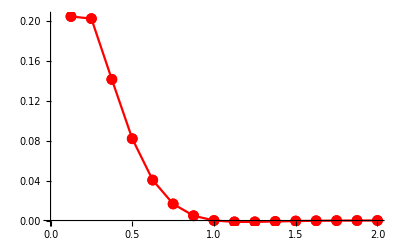

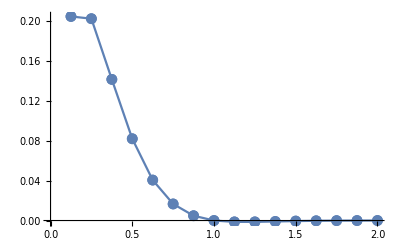

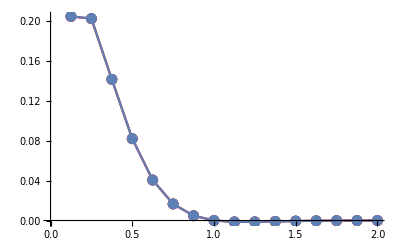

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xi[[i]],Ui1[[i]]},{i,2,2^j+1}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xi[[i]],correctu[[i]]},{i,2,2^j+1}],Mesh->Full]
(*对比图*)
Show[img1,img2]
```

```mathematica
delta=0.0001;
epsilon=0.1;
lamuda=-0.01;
Clear[f,g0,g2];
f[x_]:=E^(-5 x) Sin[Pi x];
(*f[x_]:=E^(-(x-2)^2/8);*)
g0[t_]:=Sqrt[20/(20+t)]*E^(-(5+4t)^2/10/(t+20));
g2[t_]:=Sqrt[20/(20+t)]*E^(-2 (5+2t)^2/5/(t+20));
j=5;
xi=Table[i 2/2^j,{i,0,2^j}];
U0=f[xi];
V=Table[-epsilon wdx[j,2 (k-n)/2^j]+lamuda wd2x[j,2 (k-n)/2^j],{k,1,2^j+1},{n,1,2^j+1}];
K1=V.U0;
K2=V.(U0+K1/2);
K3=V.(U0+(Sqrt[2]-1)/2 K1+(Sqrt[2]+1)/2 K2);
K4=V.(U0-Sqrt[2]/2 K2+(2+Sqrt[2])/2 K3);
Ui1=U0+delta/6 (K1+(2-Sqrt[2]) K2+(2+Sqrt[2]) K3+K4);
(*精确解*)
Clear[u3];
u3[x_,t_]:=E^(-5 x+t (-0.01 (25-Pi^2)+0.5)) Sin[Pi x];
correctu=u3[xi,0.001];
list=Table[{N[xi[[i]]],correctu[[i]],Ui1[[i]],Abs[correctu[[i]]-Ui1[[i]]]},{i,2,2^j+1}];
PrependTo[list,{"x","精确解","小波数值解","误差值"}];
GridBox[list,ColumnAlignments->Center,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

x | 精确解 | 小波数值解 | 误差值
0.0625 | 0.142781 | 0.151452 | 0.0086707
0.125 | 0.204907 | 0.213577 | 0.00867018
0.1875 | 0.21764 | 0.226737 | 0.00909669
0.25 | 0.20266 | 0.21178 | 0.00911941
0.3125 | 0.174346 | 0.180927 | 0.00658091
0.375 | 0.141731 | 0.148603 | 0.00687232
0.4375 | 0.110079 | 0.11385 | 0.00377049
0.5 | 0.0821136 | 0.0864371 | 0.00432346
0.5625 | 0.0589213 | 0.0606116 | 0.00169034
0.625 | 0.0406066 | 0.0430696 | 0.00246297
0.6875 | 0.0267369 | 0.0271772 | 0.000440371
0.75 | 0.0166354 | 0.0179758 | 0.00134042
0.8125 | 0.00956245 | 0.0093798 | 0.000182646
0.875 | 0.00481895 | 0.00556343 | 0.000744474
0.9375 | 0.00179735 | 0.00137541 | 0.000421937
1. | 0. | 0.000458507 | 0.000458507
1.0625 | -0.00096205 | -0.00142481 | 0.000462756
1.125 | -0.00138065 | -0.00105074 | 0.000329916
1.1875 | -0.00146645 | -0.0018853 | 0.00041885
1.25 | -0.00136551 | -0.0010959 | 0.000269612
1.3125 | -0.00117474 | -0.00152393 | 0.000349195
1.375 | -0.000954975 | -0.000722358 | 0.000232618
1.4375 | -0.000741709 | -0.00102054 | 0.000278826
1.5 | -0.000553277 | -0.000354142 | 0.000199135
1.5625 | -0.000397008 | -0.00061158 | 0.000214572
1.625 | -0.000273605 | -0.000112494 | 0.000161111
1.6875 | -0.000180152 | -0.00033427 | 0.000154118
1.75 | -0.000112088 | 1.36506×10^-6 | 0.000113453
1.8125 | -0.0000644313 | -0.000153368 | 0.0000889365
1.875 | -0.0000324699 | 0.0000149977 | 0.0000474676
1.9375 | -0.0000121104 | -0.0000255104 | 0.0000134
2. | 0. | -9.42527×10^-6 | 9.42527×10^-6

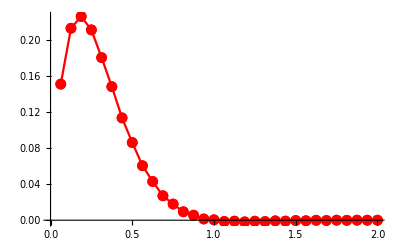

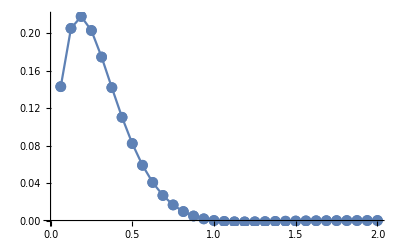

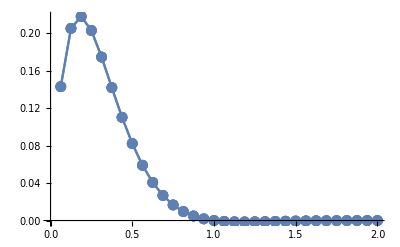

```mathematica
(*数值解绘图*)
img1=ListLinePlot[Table[{xi[[i]],Ui1[[i]]},{i,2,2^j+1}],Mesh->Full,PlotStyle->{Red}]
(*精确解绘图*)
img2=ListLinePlot[Table[{xi[[i]],correctu[[i]]},{i,2,2^j+1}],Mesh->Full]
(*对比图*)
Show[img2,img2]
```